# Variational Quantum Eigensolver: Transverse-Field Ising Model

In this demonstration, we calculate the ground-state energy of the transverse-field Ising model,

H=J(Σ_(k=1)^(n-1)Z_k Z_(k+1)+B Σ_(k=1)^n X_k) ,

where X_k and Z_k are the Pauli X and Z operators, respectively, acting on qubit k, J is the exchange energy, and B is the dimensionless field in the transverse direction (that is, along the x-axis).

The model exhibits a quantum phase transition from the ferromagnetic (or ordered) phase (|B|<1) to the paramagnetic (or disordered) phase (|B|<1).

FindMinimum | Searches for a local mininum
QuantumCircuit | Quantum circuit model
XXXX | XXXX

Functions used in variational quantum eigensolver.

## Preliminary

Make sure that the Q3 package is loaded.

```mathematica
<<Q3`
```

This function checks the calculated value against the true ground-state energy. It returns a pair {val,error} of the estimated ground-state energy val and the error relative to the true ground-state energy.

```mathematica
checkResult[val_,true_]:=With[
{error=Abs@PseudoDivide[val-true,true]},
If[error>10*^-2,Message[checkResult::big]];
{val,PercentForm@error}
]
checkResult::big="The error is too big!";
```

## Setting Up the Model

Take a quantum register of n qubits. We refer to the register by symbol S.

```mathematica
Let[Qubit,S]
```

```mathematica
$n=4;
kk=Range[$n];
SS=S[kk,$]
```

{S_(,,1),S_(,,2),S_(,,3),S_(,,4)}

Take the Hamiltonian of transverse-field Ising model. We have put J=1. In other words, we measure energies in units of J. On the other hand, B is the dimensionless field in the transverse direction.

```mathematica
Let[Real,B]
HH=Total@ChainBy[Through[SS[3]],Multiply]+B*Total@Through[SS[1]]
```

S_(,,1)^(,,Z)S_(,,2)^(,,Z)+S_(,,2)^(,,Z)S_(,,3)^(,,Z)+S_(,,3)^(,,Z)S_(,,4)^(,,Z)+B (S_(,,1)^(,,X)+S_(,,2)^(,,X)+S_(,,3)^(,,X)+S_(,,4)^(,,X))

## Elementary Quantum Circuit Layer

A variational quantum circuit is usually constructed by accumulating layers of quantum circuits. Here, we construct an elementary quantum circuit layer to be used repeatedly later.

The variational parameters are denoted by a[layer,qubit,μ].

```mathematica
Let[Real,a]
```

Construct a basic layer of quantum circuit.

```mathematica
Clear[rot,layer]
rot[k_]=QuantumCircuit@Table[EulerRotation[Pi*a[k,q,{1,2,3}],S[q,$]],{q,$n}];
cnt=QuantumCircuit[
CNOT@@@Partition[SS,2],
CNOT@@@Partition[Rest@SS,2]
];
layer[k_Integer]=QuantumCircuit[rot[k],cnt];
layer[kk:{___Integer}]:=QuantumCircuit@@Riffle[Table[layer[k],{k,kk}],"Separator"]
```

For example, here is a variational quantum circuit with two layers. Although all boxes are denoted by the same label U_E, they represent different Euler rotations with different sets of Euler angles  {a[layer,qubit,1],a[layer,qubit,2],a[layer,qubit,3]}.

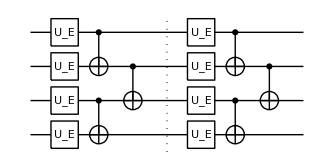

```mathematica
layer[{1,2}]
```

## Variational Quantum Circuit (Ansatz)

Here, we construct a variational quantum circuit by accumulating the quantum circuit layers defined above.

The number of layers.

```mathematica
$L=2;
```

Construct a variational quantum circuit.

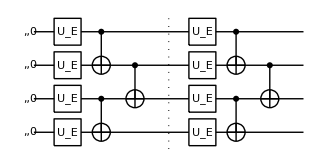

```mathematica
try=QuantumCircuit[Ket[SS],layer[Range@$L]]
```

The above quantum circuit involves L×n×3 variational parameters a_(l,q,μ) for layer l, qubit q, and μ=1,2,3.

```mathematica
aa=a[Range@$L,kk,{1,2,3}]
```

{a_(,,111),a_(,,112),a_(,,113),a_(,,121),a_(,,122),a_(,,123),a_(,,131),a_(,,132),a_(,,133),a_(,,141),a_(,,142),a_(,,143),a_(,,211),a_(,,212),a_(,,213),a_(,,221),a_(,,222),a_(,,223),a_(,,231),a_(,,232),a_(,,233),a_(,,241),a_(,,242),a_(,,243)}

This is to randomly initialize the parameters.

```mathematica
a0=Flatten@RandomReal[{0,1}Pi,{$L,$n,3}]
```

{0.277257,2.84767,2.52498,0.459343,1.37404,1.44009,0.648646,1.96785,0.281691,1.95775,2.57671,1.06928,2.06934,2.32917,2.22022,1.44872,2.0265,3.01477,1.56555,1.38174,2.55172,0.0079894,0.511057,1.23075}

Evaluate the quantum circuit to express it in the vector form.

```mathematica
EchoTiming[out=Matrix[try,SS];]
```

0.327351

## Variational Solution in the Paramagnetic Phase

Now, we are ready to solve the variational problem by defining the objective function and minimizing the function over the variational parameter. Here, we first solve the problem in the paramagnetic phase.

Construct the objective function, which in this case is the expectation value of the Hamiltonian.

```mathematica
Block[
{B=5.}, (*Paramagnetic phase*)
EchoTiming[mat=Matrix[HH,SS]];
Echo[groundStateEnergy=Min@Eigenvalues[mat],"Ground-state energy"];
EchoTiming[avg=Re[Conjugate[out].mat.out]];
]
```

0.003368

Ground-state energy  -20.1501

0.079211

A variable to take trace of the value of objective function at each iteration step.

```mathematica
data={};
```

Iteratively calculate the ground-state energy by minimizing the expectation value of the Hamiltonian.

```mathematica
{val,sol}=FindMinimum[avg,Transpose@{aa,a0},
StepMonitor:>(
AppendTo[data,avg];
PrintTemporary["Expectation value: ",avg]
),
Method->"IPOPT"];
```

Check the result. The first value is the estimation of the ground-state energy and the second number is the relative error.

```mathematica
checkResult[val,groundStateEnergy]
```

{-20.1,0.2488%}

This shows the convergence behavior of the above iteration method.

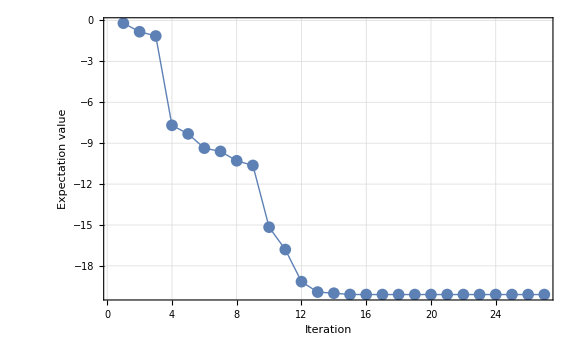

```mathematica
ListLinePlot[data,
PlotMarkers->{"●", 12},
PlotRange->All,
FrameLabel->{"Iteration",Expectation value}]
```

## Variational Solution in the Ferromagnetic Phase

Here, we solve the variational problem by minimizing the expectation value of the Hamiltonian in the paramagnetic phase.

Construct the objective function, which in this case is the expectation value of the Hamiltonian.

```mathematica
Block[
{B=0.2}, (*Ferromagnetic phase*)
EchoTiming[mat=Matrix[HH,SS]];
Echo[groundStateEnergy=Min@Eigenvalues[mat],"Ground-state energy"];
EchoTiming[avg=Re[Conjugate[out].mat.out]];
]
```

0.003221

Ground-state energy  -3.06173

0.080906

A variable to take trace of the value of objective function at each iteration step.

```mathematica
data={};
```

Iteratively calculate the ground-state energy by minimizing the expectation value of the Hamiltonian.

```mathematica
{val,sol}=FindMinimum[avg,Transpose@{aa,a0},
StepMonitor:>(
AppendTo[data,avg];
PrintTemporary["Expectation value: ",avg]
),
Method->"IPOPT"];
```

Check the result. The first value is the estimation of the ground-state energy and the second number is the relative error.

```mathematica
checkResult[val,groundStateEnergy]
```

{-3.05946,0.0743%}

This shows the convergence behavior of the above iteration method.

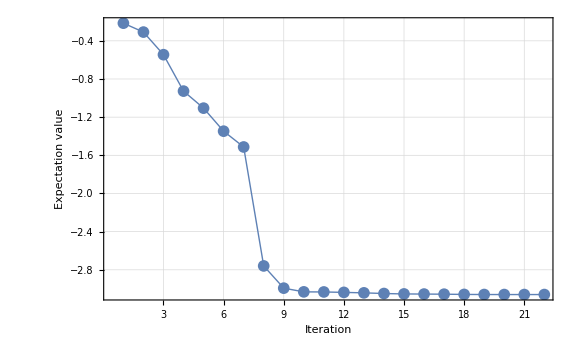

```mathematica
ListLinePlot[data,
PlotMarkers->{"●", 12},
PlotRange->All,
FrameLabel->{"Iteration",Expectation value}]
```

Related Guides

Quantum Information Systems

Quantum Many-Body Systems

Quantum Spin Systems

Related Tech Notes

A Quantum Playbook

Quantum Information Systems with Q3

Quantum Many-Body Systems with Q3

Quantum Spin Systems with Q3

Related Links

Mahn-Soo Choi (2022), A Quantum Computation Workbook (Springer, 2022).

## Metadata

### Categorization

Tech Note

QuantumPlaybook

QuantumPlaybook`

QuantumPlaybook/tutorial/VariationalQuantumEigensolverTransverseFieldIsingModel

### Keywords

variational quantum algorithm

variational quantum eigensolver

VQA

VQE